## Drawing Lattice

### Function Definitions

Draws the basic motif (unit cell) to be translated :

```mathematica
(* Default Style Values *)
ResetStyles:=(
AtomColor=Black; LineColor = Black;  AtomSize = 0.02; MotifOpacity=1;
)
ResetStyles;

(* Function Definiton *)
Clear[Motif];
Motif[root_,atoms_,links_,θ_:0]:=Graphics[{
Opacity[MotifOpacity],
LineColor,Rotate[Line/@ Map[(root+#)& ,links,{2}],θ,root],
PointSize[AtomSize],AtomColor,Rotate[Point /@ Map[(root+#)& ,atoms],θ,root]
}]

(* Note: it is better to define separate motifs for atoms and links, thereby avoiding layering issues *)
```

Applies the elementary translations to the root point. Returns a flat array with all the generated points:

```mathematica
Clear[Lattice2D];
Lattice2D[root_List,ai_List,size_List,θ_:0]:=(root+#)&/@ RotationTransform[θ]/@Flatten[
Table[
p ai⟦1⟧+q ai⟦2⟧,{p,-size⟦1⟧,size⟦1⟧},{q,-size⟦2⟧,size⟦2⟧}
]
,1]
```

### Square Lattice:

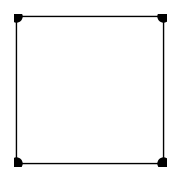

```mathematica
Nroot = {0,0}; AtomSize = 0.05;
Show[Motif[Nroot,{{0,0},{0,1},{1,0},{1,1}},{{{0,0},{0,1}},{{0,0},{1,0}},{{1,0},{1,1}},{{0,1},{1,1}}}],ImageSize-> Small]
```

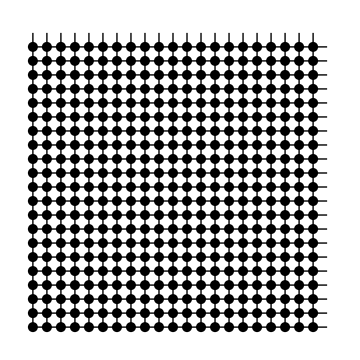

```mathematica
ResetStyles;
Motif[#,{{0,0}},{{{0,0},{0,1}},{{0,0},{1,0}}}]&/@Lattice2D[Nroot,{{1,0},{0,1}},{10,10}];
Show[%,ImageSize-> Medium]
```

### Graphene

```mathematica
δ0={0,0};δ1={(√3)/2,-1/2};δ2={0,1};δ3={-(√3)/2,-1/2};
a1=√3{-1/2,(√3)/2}; a2=√3{1/2,(√3)/2};
```

```mathematica
(* Origin *)
Nroot={0,0};  
(* Atom Positions w.r.t origin *)
Natoms={δ0,δ2};   
(* The lines connecting neighbors *)
Nlinks={{δ0,δ2},{δ2,δ2-δ3},{δ2,δ2-δ1}};
```

Now just apply the two functions defined above to generate the lattice, and apply the motif to each lattice point :

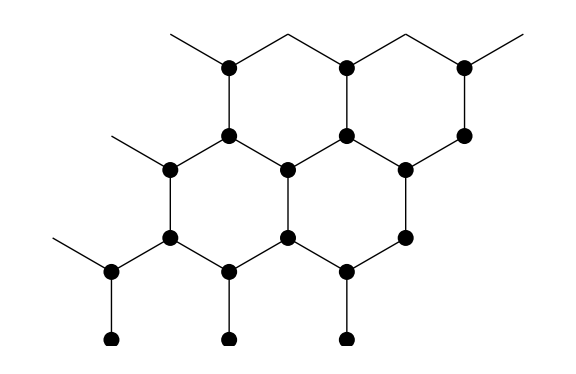

```mathematica
ResetStyles;
Motif[#,Natoms,Nlinks]&/@ Lattice2D[Nroot,{a1-a2,a2},{1,1}];
HC1=Show[%,ImageSize->Large]
```

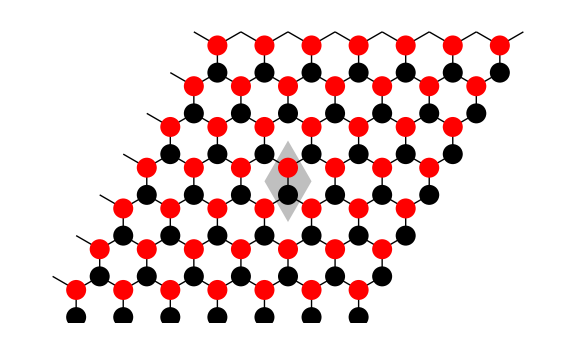

```mathematica
(* The first sublattice *)
AtomSize=0.025;AtomColor=Black;MotifOpacity=1;
SubLat1=Motif[#,{δ0},Nlinks]&/@ Lattice2D[Nroot,{a1-a2,a2},{3,3}];
(* The second sublattice *)
AtomColor=Red;
SubLat2=Motif[#,{δ2},{}]&/@ Lattice2D[Nroot,{a1-a2,a2},{3,3}];
(* The primitive cell *)
UnitCell = Graphics[{Opacity[0.5],Gray,Polygon[{{δ0-δ2,a1-δ2,a1+a2-δ2,a2-δ2}}]}];
Show[UnitCell,SubLat1,SubLat2,ImageSize->Large]
```